# Testes com splines clássicas e Q-splines

## Definições das splines (versões clássica e Q)

### Splines clássicas

```mathematica
(* Definição das bases clássicas de Hermite -----------------------------------*)
(* Versão condensada *)
He[n_][x_]:=Expand[  (-1)^n ⅇ^(x^2/2) D[ⅇ^(-x^2/2),{x,n}]  ];

(* Versão recursiva *)
Hp[n_][x_]:=Expand[If[n==0, 1, If[n==1, x,  x*Hp[n-1][x]-(n -1)* Hp[n-2][x]]]];

(* Base de Hermite para os polinômios cúbicos *)
Hermite3[x_]:=Table[Hp[i-1][x],{i, 4}];

(* Definição da spline de hermite no formato tensorial -------------------------*)
St[C_,x_]:=C.Hermite3[x];
MH={{-2,6,-3,2},
{3,-6,3,-2},
{-2,4,-2,1},
{-1,3,-1,1}};
SplineHermite[P_, t_]:=St[P.MH,t]; (* A multiplicação por MH ajusta os coeficientes da spline (descreve-os em termos do vetor de restrições) *)

(* Definição da curva clássica da spline no domínio [a, b]. --------------------*)
(* Essa versão supõe os pontos possivelmente desigualmente espaçados. *)
SNH[P_,n_,spline_,x_]:= (
answer=0;
For[i=1; found=0;,i≤n,i++,
(*Print["i=",i];Print["   Pi=",P[[i]]];Print["   Pi+1=",P[[i+1]]];*)
If[ (i<Length[P])&&(P[[i]]≤ x<  P[[i+1]]),
(*Print["found=",1];*)
found=1;
answer = spline[(x-P[[i]])/(P[[i+1]]-P[[i]])][[i]];(* Transformação de coordenadas em X, para o domínio t em [0,1] *)
]
If[found==1,Break[]]
(*If[i==n && found==0,0]*)
];
(*Print [Answer];*)
Return [answer];
);

(* Fórmula para calcular o RMSE entre dois conjuntos de pontos *)
RMSE[A_,B_]:=(k=Length[A];Return[1/(k)*√(∑_(i=1)^k (A[[i]]-B[[i]])^2)];);
```

### Q-Splines

```mathematica
(* Versão pré-calculada da Q-Base de Hermite de grau 3 (notebook do Mathematica: '1DTensorBSplines.nb'). *)
QHermite3n[q_,t_]:={4^(1/(-1+q)) (4-(-1+q)^2 t^4)^(1/(1-q)),
4^(1/(-1+q)) t (4-(-1+q)^2 t^4)^(1/(1-q)),
-2^(-1+2/(-1+q)) (2+(-3+q) t^2) (4-(-1+q)^2 t^4)^(1/(1-q)),
2^(-1+2/(-1+q)) t (-8+2 q+(-3+q) (-2+q) t^2) (4-(-1+q)^2 t^4)^(1/(1-q))};

(* Versão pré-calculada da Q-Spline de grau 3 e de sua Q-Derivada primeira (notebook do Mathematica: '1DTensorBSplines.nb'). *)
QS3[q_,t_]:=2^(-1+2/(-1+q)) (4-(-1+q)^2 t^4)^(1/(1-q)) (2 Subscript[a, 0]+2 t Subscript[a, 1]-(2+(-3+q) t^2) Subscript[a, 2]+t (2 (-4+q)+(-3+q) (-2+q) t^2) Subscript[a, 3]) ;DQS1[q_,t_]:= 2^(-1+2/(-1+q)) (4-(-1+q)^2 t^4)^(q/(1-q)) (8 (-1+q) t^3 Subscript[a, 0]-2 (-4+(-5+q) (-1+q) t^4) Subscript[a, 1]+2 t (12-4 q-4 (-1+q) t^2+(-3+q)^2 (-1+q) t^4) Subscript[a, 2]+(-32+8 q+12 (-3+q) (-2+q) t^2-2 (-5+q) (-4+q) (-1+q) t^4-(-3+q) (-2+q) (-1+q) (-7+3 q) t^6) Subscript[a, 3]);

(* Cálculo dos coeficientes da Q-Spline (Subscript[a, 0],Subscript[a, 1], Subscript[a, 2],Subscript[a, 3])*)
Coeficientes=FullSimplify[Solve[{QS3[q,0]==xo, QS3[q,1]==xf,DQS1[q,0]==vo,DQS1[q,1]==vf},{Subscript[a, 0],Subscript[a, 1], Subscript[a, 2],Subscript[a, 3]}]][[1]]

(* ATENÇÃO: TODA VEZ QUE EXECUTAR, TEM QUE VERIFICAR A ORDEM. O VETOR 'Coef' tem que conter, respectivamente: {Subscript[a, 0], Subscript[a, 1], Subscript[a, 2], Subscript[a, 3]}. *)
Coef[xo_,xf_,vo_,vf_, q_]={
Coeficientes[[1,2]],Coeficientes[[3,2]],Coeficientes[[2,2]],Coeficientes[[4,2]]
};

Pesos[P_,q_]:= Coef[P[[1]], P[[2]], P[[3]], P[[4]],q]; (* Versão compacta da matriz de coeficientes em função de q. *)
QStn[A_, q_, t_] := A . QHermite3n[q, t];  (* Q-Spline tensorial *)

(* Q-Spline escrita em termos do vetor de restrições {x0, xf, vo, vf}, q e t. *)
QSplineI[P_, q_, t_] := QStn[Pesos[P,q], q, t]; 

(* Definição da curva Q-Spline no domínio [a, b]. --------------------*)
(* Essa versão supõe os pontos possivelmente desigualmente espaçados. *)
SNQ[P_,n_,spline_,q_,x_]:= (
answer=0;
For[i=1; found=0;,i≤n,i++,
(*Print["i=",i];Print["   Pi=",P[[i]]];Print["   Pi+1=",P[[i+1]]];*)
If[(i<Length[P])&&(P[[i]]≤ x<  P[[i+1]]),
(*Print["found=",1];*)
found=1;
answer = spline[q,(x-P[[i]])/(P[[i+1]]-P[[i]])][[i]];(* Transformação de coordenadas em X, para o domínio t em [0,1] *)
]
If[found==1,Break[]]
(*If[i==n && found==0,0]*)
];
(*Print [Answer];*)
Return [answer];
);
```

{a_0→(16^(1/(1-q)) (-2^((1+q)/(-1+q)) (-(-3+q) (1+q))^(q/(-1+q)) vf+2^(q/(-1+q)) (-(-3+q) (1+q))^(1/(-1+q)) (5 2^(q/(-1+q)) q+2^(1/(-1+q)) (5-3 q^2)) xf+4^(1/(-1+q)) (4^(q/(-1+q)) (-3+q^2) vo+4^(1/(-1+q)) (-8 q vo+(-3+q) (1+q) (3+q) xo))))/((-3+q)^2 (1+q)),a_2→-(2 (4^(1/(1-q)) (-(-3+q) (1+q))^(q/(-1+q)) vf+4^(1/(1-q)) (-(-3+q) (1+q))^(1/(-1+q)) (-5+q (-10+3 q)) xf-(-3+q) (1+q) (2 vo+3 xo)))/((-3+q)^2 (1+q)),a_1→1/((-3+q)^2 (-2+q) (1+q))2^(-7/(-1+q)) (-16^(1/(-1+q)) (-(-3+q) (1+q))^(q/(-1+q)) (2^(3+1/(-1+q))-2^(q/(-1+q)) q) vf-21 2^((6+q)/(-1+q)) vo+(-(-3+q) (1+q))^(1/(-1+q)) (-32^(q/(-1+q)) q^2+2^(2+5/(-1+q)) (4+15 q+q^3)) xf+128^(1/(-1+q)) (q (-7+q (25+(-9+q) q)) vo-4 (-4+q) (-3+q) (1+q) xo)),a_3→-(2 (4^(1/(1-q)) (-(-3+q) (1+q))^(q/(-1+q)) vf+2^((-3+q)/(-1+q)) (-(-3+q) (1+q))^(1/(-1+q)) (-1+(-4+q) q) xf-(-3+q) (1+q) (vo+2 xo)))/((-3+q)^2 (-2+q) (1+q))}

## Testes

### Testes usando a função fractal de Weierstrass

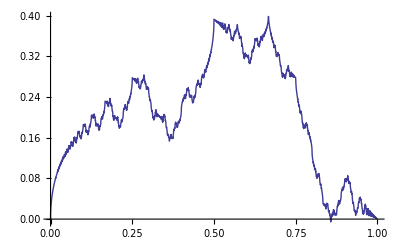

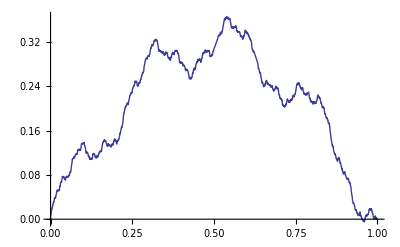

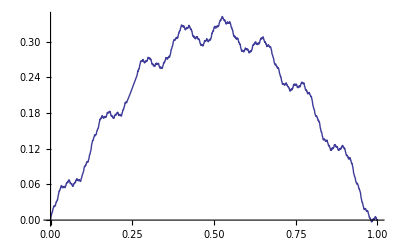

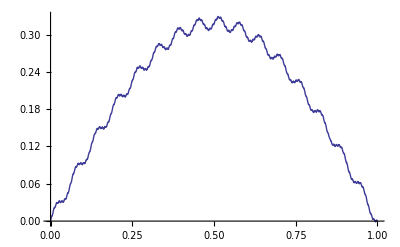

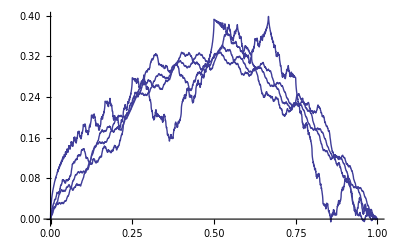

```mathematica
(* Definição da função fractal de Weierstrass (Subscript[F, a](x)=∑_(k=1)^∞ Sin[πk^a x]/(πk^a)) *)
AxesFontSize=15;
WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* k^a ]/(Pi*k^a),{k,250}]];
WS=Plot[WeierstrassFunction[2,x], {x, 0, 1}](* Visualização para k=3*)
WS1=Plot[WeierstrassFunction[3,x], {x, 0, 1}](* Visualização para k=3*)
WS2=Plot[WeierstrassFunction[4,x], {x, 0, 1}](* Visualização para k=3*)
WS3=Plot[WeierstrassFunction[5,x], {x, 0, 1}](* Visualização para k=3*)
Show[WS,WS1,WS2,WS3]
```

```mathematica
Plot[{WeierstrassFunction[2,x],WeierstrassFunction[3,x],WeierstrassFunction[4,x],WeierstrassFunction[5,x]}, {x, 0, 1},PlotStyle->{Thickness[0.002]},AxesStyle->{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]}, AxesLabel-> {"t","W_i(t)"}, PlotLegend->{Style["W_2", 15],Style["W_3", 15],Style["W_4", 15],Style["W_5", 15]},LegendPosition->{1.1,-0.4},ImageSize->{500}]
```

Plot::optx: Unknown option PlotLegend in Plot[{WeierstrassFunction[2, x], WeierstrassFunction[3, x], WeierstrassFunction[4, x], WeierstrassFunction[5, x]}, {x, 0, 1}, PlotStyle → {Thickness[0.002`]}, AxesStyle → {Directive[Black, AxesFontSize], Directive[Black, AxesFontSize]}, AxesLabel → {.

Plot[{WeierstrassFunction[2,x],WeierstrassFunction[3,x],WeierstrassFunction[4,x],WeierstrassFunction[5,x]},{x,0,1},PlotStyle→{Thickness[0.002]},AxesStyle→{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]},AxesLabel→{t,W_i(t)},PlotLegend→{W_2,W_3,W_4,W_5},LegendPosition→{1.1,-0.4},ImageSize→{500}]

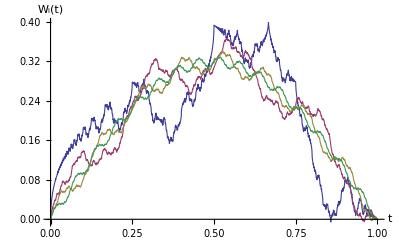

```mathematica
Plot[{WeierstrassFunction[2,x],WeierstrassFunction[3,x],WeierstrassFunction[4,x],WeierstrassFunction[5,x]}, {x, 0, 1},PlotStyle->{Thickness[0.002]},AxesStyle->{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]}, AxesLabel-> {"t","W_i(t)"}, PlotLegend->{Style["W_2", 15],Style["W_3", 15],Style["W_4", 15],Style["W_5", 15]},LegendPosition->{1.1,-0.4},ImageSize->{500}]
```

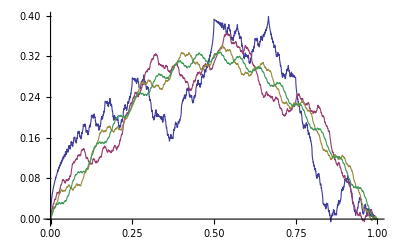

#### VERSÃO ' STANDALONE' : Um valor de Q de cada vez.

Este ensaio tem a finalidade de 'emular' mudanças de resolução, como ampliações. Dentre os gráficos gerados, os pontos em azul são emulados, e os pontos em preto são amostrados da função fractal, no caso, Weierstrass. Neste exemplo, só fizemos esse processo para um valor de Q. É possível mudar os parâmetros, que são:
- fatorEscala: representa um fator de escala da imagem, a princípio tomado como uma ampliação.
- n0: a quantidade inicial de pontos de amostragem sobre a função fractal verdadeira.
- n1: a quantidade de pontos para o qual a imagem será transformada (depende, obviamente, do fator de escala).
- k: expoente da função de Weierstrass.
-Qv: valor de Q para o qual desejamos efetuar o cálculo.

Pontos a serem interpolados:

Em X:{0,1/6,1/3,1/2,2/3,5/6,1}

Em Y:{0.,0.140886,0.304617,0.308425,0.243694,0.201809,0.}

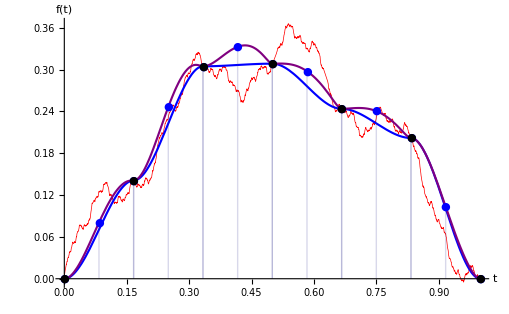

RMSE: 0.00726019

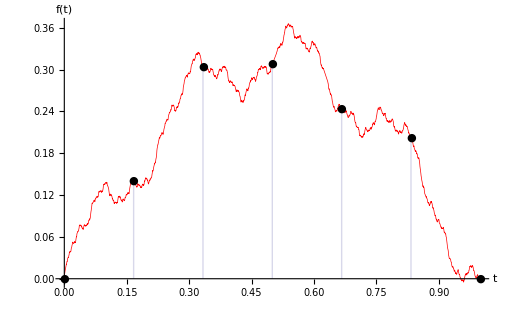

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;             (* Fator de escala *)
n0=6;                                       (* Número inicial de pontos *)
n1 = n0*fatorEscala; (* Numero final de pontos *)
k=3;                                          (* Expoente de Weierstrass *)
Qv = 2.6;                               (* Valor de q *)
AxesFontSize = 20;
(*-----------------------------------------------------------------------------*)

WS=Plot[WeierstrassFunction[k,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]},AxesStyle->{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]}, AxesLabel-> {"t","f(t)"},PlotStyle->{Thickness[0.002]}];(* Visualização para k=3*)

(* Visualização do escalamento *)
(*GeraGraficos[3,n0,Qv] (* sinal 'original' *)
GeraGraficos[3,n1,Qv] ;(* sinal 'escalado' *)*)

(* 1) Recria splines para a imagem original *)

PTX0=Table[x/n0,{x,0,n0}];
PTS0= Table[WeierstrassFunction[k,PTX0[[i]]],{i, 1, n0+1}];
PTY0= Table[WeierstrassFunction[k,PTX0[[i]]/(PTX0[[n0+1]]-PTX0[[1]])],{i, 1, n0+1}];
Print["Pontos a serem interpolados:"];
Print["Em X:",PTX0];
Print["Em Y:",PTY0];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica0[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,n0}];
QSpline0[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,n0}];

(* 3) Visualização dos pontos iniciais de interpolação *)
points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, n0+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/n1,{x,0,n1}];
PTS1= Table[WeierstrassFunction[k,PTX1[[i]]],{i, 1, n1+1}];
PTY1= Table[SNQ[PTX0,n1,QSpline0,Qv,PTX1[[i]]/(PTX1[[n1+1]]-PTX1[[1]])],{i, 1, n1+1}];
points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, n1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];

(* 5) Visualização da spline clássica *)
spC0 = Plot[{SNH[PTX0,n1,splineClassica0,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]},AxesStyle->{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]}, AxesLabel-> {"t","W_i(t)"}];
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
spC1 = Plot[{SNQ[PTX0,n1,QSpline0,Qv,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]},AxesStyle->{Directive[Black,AxesFontSize],Directive[Black,AxesFontSize]}, AxesLabel-> {"t","W_i(t)"}];
Show[WS,spC0,spC1,points1,points0]
Print["RMSE: ", RMSE[PTS1,PTY1]]
Show[WS,points0]

(*Plot[{SNQ[PTX1,n*fatorEscala,qspline,Qp,x]},{x,0,n*fatorEscala},PlotStyle->{Purple,Thickness[0.003]}]*)
```

#### VERSÃO ' MULTI' : Vários valores de Q.

Este ensaio tem a finalidade de 'emular' mudanças de resolução, como ampliações. Dentre os gráficos gerados, os pontos em azul são emulados, e os pontos em preto são amostrados da função fractal, no caso, Weierstrass. Neste exemplo, é possível realizar esse processo para vários valores de Q. É ainda possível mudar os parâmetros, que são:
- fatorEscala: representa um fator de escala da imagem, a princípio tomado como uma ampliação.
- k0: expoente da função de Weierstrass.
- NI: a quantidade inicial de pontos de amostragem sobre a função fractal verdadeira.
- NF: a quantidade final de pontos a serem tomados como ponto de partida para amostragem sobre a função fractal verdadeira.
- incrementoN: o passo de incremento para as quantidades iniciais de pontos a serem avaliados.
- QI: valor inicial para Q.
- QF: valor final para Q.
- incrementoQ: valor do passo de incremento para Q.

Este trecho de código tem a finalidade de oferecer uma visualização da curva durante o processo de interpolação.

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 3;             (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=3;                                          (* Expoente de Weierstrass *)

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =5;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.4001;
(*-----------------------------------------------------------------------------*)

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
Print["k=",k0 ,", ni=",ni];
For[qi = QI,qi≤QF,qi+=incrementoQ,
Print[];
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)

WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];

(* 5) Visualização da spline clássica *)
spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];

(* 6) Visualização da Q-spline *)
spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];
Print["  Q=",qi];
Print["  RMSE: ", RMSE[PTS1,PTY1]];
(*Show[WS,spC0,spC1,points1,points0]//Print;*)
];
];


(*Plot[{SNQ[PTX1,n*fatorEscala,qspline,Qp,x]},{x,0,n*fatorEscala},PlotStyle->{Purple,Thickness[0.003]}]*)
```

k=3, ni=3

Q=-0.8

RMSE: 0.106923

Q=-0.3999

RMSE: 0.019111

Q=0.0002

RMSE: 0.0134344

Q=0.4003

RMSE: 0.0124929

Q=0.8004

RMSE: 0.0121725

Q=1.2005

RMSE: 0.0119853

Q=1.6006

RMSE: 0.0118196

Q=2.0007

RMSE: 0.0116036

Q=2.4008

RMSE: 0.011236

Q=2.8009

RMSE: 0.0129039

k=3, ni=4

Q=-0.8

RMSE: 0.0935469

Q=-0.3999

RMSE: 0.0147342

Q=0.0002

RMSE: 0.00927765

Q=0.4003

RMSE: 0.00841837

Q=0.8004

RMSE: 0.00816576

Q=1.2005

RMSE: 0.00803991

Q=1.6006

RMSE: 0.00793812

Q=2.0007

RMSE: 0.00780904

Q=2.4008

RMSE: 0.00766677

Q=2.8009

RMSE: 0.0107898

k=3, ni=5

Q=-0.8

RMSE: 0.0881569

Q=-0.3999

RMSE: 0.0156572

Q=0.0002

RMSE: 0.0102846

Q=0.4003

RMSE: 0.00937236

Q=0.8004

RMSE: 0.0091735

Q=1.2005

RMSE: 0.00914754

Q=1.6006

RMSE: 0.00915675

Q=2.0007

RMSE: 0.00911411

Q=2.4008

RMSE: 0.00886967

Q=2.8009

RMSE: 0.00975687

#### VERSÃO ' MULTI' 2: Vários valores de Q.

Este ensaio tem a finalidade de 'emular' mudanças de resolução, como ampliações. Dentre os gráficos gerados, os pontos em azul são emulados, e os pontos em preto são amostrados da função fractal, no caso, Weierstrass. Neste exemplo, é possível realizar esse processo para vários valores de Q. É ainda possível mudar os parâmetros, que são:
- fatorEscala: representa um fator de escala da imagem, a princípio tomado como uma ampliação.
- k0: expoente da função de Weierstrass.
- NI: a quantidade inicial de pontos de amostragem sobre a função fractal verdadeira.
- NF: a quantidade final de pontos a serem tomados como ponto de partida para amostragem sobre a função fractal verdadeira.
- incrementoN: o passo de incremento para as quantidades iniciais de pontos a serem avaliados.
- QI: valor inicial para Q.
- QF: valor final para Q.
- incrementoQ: valor do passo de incremento para Q.

Este trecho de código tem a finalidade de oferecer um vislumbre NUMÉRICO acerca do erro RMSE durante o processo de interpolação.

k=3, ni=3

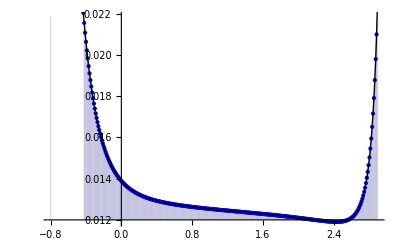

k=3, ni=4

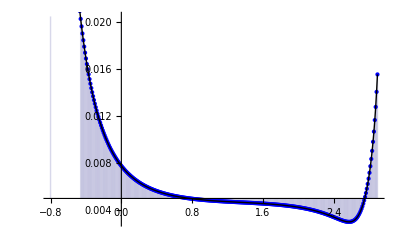

k=3, ni=5

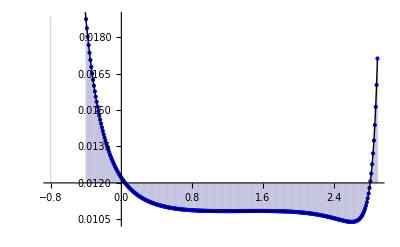

k=3, ni=6

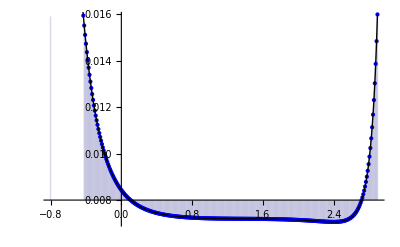

k=3, ni=7

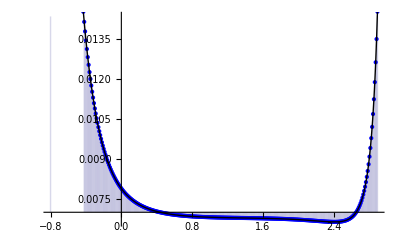

k=3, ni=8

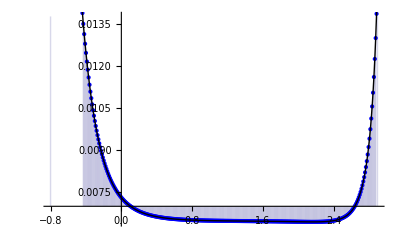

k=3, ni=9

$Aborted

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;             (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=3;                                          (* Expoente de Weierstrass *)

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =10;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.01001;
(*-----------------------------------------------------------------------------*)

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
Print["k=",k0 ,", ni=",ni];
(* Limpa as listas *)
QValues={};
RMSEValues={};
plotlist={};
For[qi = QI,qi≤QF,qi+=incrementoQ,
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)
(*Clear[WeierstrassFunction,PTX0,PTS0,PTY0,splineClassica,QSpline,points0,PTX1,PTS1,PTY1,points1,spC0,spC1];*)

(*WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* b^a ]/(Pi*b^a),{b,250}]];*)
(*WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
(*points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];*)

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
(*points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];*)

(* 5) Visualização da spline clássica *)
(*spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];*)
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
(*spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];*)

(*Print["  Q=",qi,", RMSE: ", RMSE[PTS1,PTY1]];*)

(*Show[WS,spC0,spC1,points1,points0]//Print;*)
QValues = Append[QValues,qi];
res =RMSE[PTY1,PTS1];
RMSEValues= Append[RMSEValues,res];
plotlist= Append[plotlist,{qi, res}];
(*Print[plotlist]*)
];

Show[ ListPlot[plotlist,Filling->Axis,PlotStyle->{Blue}] ,
Graphics[Line[plotlist]]]//Print;
];


(*Plot[{SNQ[PTX1,n*fatorEscala,qspline,Qp,x]},{x,0,n*fatorEscala},PlotStyle->{Purple,Thickness[0.003]}]*)
```

```mathematica
·
```

#### VERSÃO ' MULTI' 2: Vários valores de Q.

Este ensaio tem a finalidade de 'emular' mudanças de resolução, como ampliações. Dentre os gráficos gerados, os pontos em azul são emulados, e os pontos em preto são amostrados da função fractal, no caso, Weierstrass. Neste exemplo, é possível realizar esse processo para vários valores de Q. É ainda possível mudar os parâmetros, que são:
- fatorEscala: representa um fator de escala da imagem, a princípio tomado como uma ampliação.
- k0: expoente da função de Weierstrass.
- NI: a quantidade inicial de pontos de amostragem sobre a função fractal verdadeira.
- NF: a quantidade final de pontos a serem tomados como ponto de partida para amostragem sobre a função fractal verdadeira.
- incrementoN: o passo de incremento para as quantidades iniciais de pontos a serem avaliados.
- QI: valor inicial para Q.
- QF: valor final para Q.
- incrementoQ: valor do passo de incremento para Q.

Este trecho de código tem a finalidade de oferecer um vislumbre NUMÉRICO acerca do erro RMSE durante o processo de interpolação.

k=2, ni=3, cor=-Graphics-

Mínimo em Q= 2.87: [0.027591]. Valor para Q=1: [0.0335893], relação V1/Vq = 1.2174

k=2, ni=4, cor=-Graphics-

Mínimo em Q= -0.249999: [0.0235825]. Valor para Q=1: [0.0251108], relação V1/Vq = 1.06481

k=2, ni=5, cor=-Graphics-

Mínimo em Q= 2.89: [0.00511694]. Valor para Q=1: [0.0175184], relação V1/Vq = 3.42361

k=2, ni=6, cor=-Graphics-

Mínimo em Q= 1.77: [0.00996744]. Valor para Q=1: [0.0100272], relação V1/Vq = 1.00599

k=2, ni=7, cor=-Graphics-

Mínimo em Q= 2.21: [0.0108127]. Valor para Q=1: [0.0109164], relação V1/Vq = 1.00959

k=2, ni=8, cor=-Graphics-

Mínimo em Q= 0.320001: [0.00548224]. Valor para Q=1: [0.00550489], relação V1/Vq = 1.00413

k=2, ni=9, cor=-Graphics-

Mínimo em Q= 2.33: [0.00936063]. Valor para Q=1: [0.00946726], relação V1/Vq = 1.01139

k=2, ni=10, cor=-Graphics-

Mínimo em Q= 2.25: [0.0065325]. Valor para Q=1: [0.00670895], relação V1/Vq = 1.02701

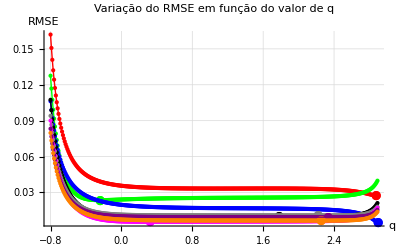

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;            (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=2;                                      (* Expoente de Weierstrass *)
fontsize=15;

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =10;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.01000001;
(*-----------------------------------------------------------------------------*)

graficos ={};
colors={Red,  Green,  Blue,  Black,  Gray,   Magenta,   Purple,  Orange,  Pink,  
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};

colors2={Red,  Green,  Blue,  Black,  Gray,  Cyan,  Magenta,  Yellow,  Brown,  Orange,  Pink,  Purple,
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};
numColors=Length[colors];
currentColor=1;

RMSList={};

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
colorMark=Graphics[ListPlot[{{0,0}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{"●"},Axes->False,ImageSize->{20,20} ]];
Print["k=",k0 ,", ni=",ni, ", cor=",colorMark ];
(* Limpa as listas *)
QValues={};
RMSEValues={};
plotlist={};
minimo = 10000;
qMinValue=0;
minimo1=10000;
qVectorIndex = 1;
For[qi = QI,qi≤QF,qi+=incrementoQ,
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)
(*Clear[WeierstrassFunction,PTX0,PTS0,PTY0,splineClassica,QSpline,points0,PTX1,PTS1,PTY1,points1,spC0,spC1];*)

(*WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* b^a ]/(Pi*b^a),{b,250}]];*)
(*WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
(*points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];*)

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
(*points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];*)

(* 5) Visualização da spline clássica *)
(*spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];*)
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
(*spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];*)

(*Print["  Q=",qi,", RMSE: ", RMSE[PTS1,PTY1]];*)

(*Show[WS,spC0,spC1,points1,points0]//Print;*)
QValues = Append[QValues,qi];
res =RMSE[PTY1,PTS1];

RMSEValues= Append[RMSEValues,res];

plotlist= Append[plotlist,{qi, res}];
(*Print[plotlist]*)
(*Print[RMSEValues]*)
(*Print["Comparando minimo =[",minimo,"] e RMSEValues[",qVectorIndex,"]=[",RMSEValues[[qVectorIndex]],"]"];*)
If[qVectorIndex == 1,
minimo=RMSEValues[[qVectorIndex]];
qMinValue = qi;
(*Print["    qi==QI"];*)
,
If[minimo>RMSEValues[[qVectorIndex]],
(*Print["    Minimo>RMSEValues[qVectorIndex]"];*)
minimo = RMSEValues[[qVectorIndex]];
qMinValue = qi;
,
(*Print["    OK: Minimo<RMSEValues[qi]"];*)
];
];

If[(minimo1==10000 )&& Round[qi]==1,
minimo1 = RMSEValues[[qVectorIndex]];
,];
(*Print["    minimo=",minimo];*)
qVectorIndex++;
];

(*minimo = Min[RMSEValues];*)

Print["     Mínimo em Q= ", qMinValue,": [", minimo,"]. Valor para Q=1: [",minimo1,"], relação V1/Vq = ",(minimo1/minimo)];
colorMark=Graphics[ListPlot[{{qMinValue,minimo}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{Style["●",fontsize-3]},Axes->False,ImageSize->{20,20} ]];

(*gi={ListPlot[plotlist,Filling->Axis,PlotStyle->{Thickness[0.002],colors[[currentColor]]},PlotRange->All,AxesOrigin->{0,0}] ,colorMark, Graphics[{colors[[currentColor]],Line[plotlist]}, PlotRange->{{QI-incrementoQ, QF+incrementoQ},{0,0.0023}},AxesOrigin->{0,0}, AxesLabel->{Style["q",fontsize-5], Style["RMSE",fontsize-5]},PlotStyle->{Thickness[0.002]},AxesStyle->{Directive[Black,24],Directive[Black,24]}}];*)
gi={ListPlot[plotlist,GridLines->Automatic,PlotLabel->"Variação do RMSE em função do valor de q",PlotStyle->{colors[[currentColor]]},PlotRange->All,AxesOrigin->{0,0}] ,colorMark, Graphics[{colors[[currentColor]],Line[plotlist]}, PlotRange->{{QI-incrementoQ, QF+incrementoQ},{0,0.0023}},AxesOrigin->{0,0}]};
(*Removida a opção Filling->Axis *)
graficos = Append[graficos, gi];
RMSList = Append[RMSList,RMSEValues];(* Salva a lista de RMSE para cada valor de N (ni). *)
(*Show[ ListPlot[plotlist,Filling->Axis,PlotStyle->{Blue}] ,
Graphics[Line[plotlist]]]//Print;*)
currentColor += 1;
];
Show[graficos, AxesLabel->{Style["q",fontsize], Style["RMSE",fontsize]},AxesStyle->{Directive[Black,fontsize],Directive[Black,fontsize]}]
```

```mathematica
Show[graficos, AxesLabel->{Style["q",fontsize], Style["RMSE",fontsize]},AxesStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic]
```

k=3, ni=3, cor=-Graphics-

Mínimo em Q= 2.43: [0.0119026]. Valor para Q=1: [0.0128284], relação V1/Vq = 1.07778

k=3, ni=4, cor=-Graphics-

Mínimo em Q= 2.57: [0.00300427]. Valor para Q=1: [0.00539502], relação V1/Vq = 1.79578

k=3, ni=5, cor=-Graphics-

Mínimo em Q= 2.6: [0.0103947]. Valor para Q=1: [0.0110156], relação V1/Vq = 1.05974

k=3, ni=6, cor=-Graphics-

Mínimo em Q= 2.4: [0.0070602]. Valor para Q=1: [0.00736263], relação V1/Vq = 1.04284

k=3, ni=7, cor=-Graphics-

Mínimo em Q= 2.41: [0.00663933]. Valor para Q=1: [0.00695778], relação V1/Vq = 1.04797

k=3, ni=8, cor=-Graphics-

Mínimo em Q= 2.16: [0.00644355]. Valor para Q=1: [0.00657967], relação V1/Vq = 1.02112

k=3, ni=9, cor=-Graphics-

Mínimo em Q= 2.21: [0.00370079]. Valor para Q=1: [0.00397873], relação V1/Vq = 1.0751

k=3, ni=10, cor=-Graphics-

Mínimo em Q= 2.09: [0.00348461]. Valor para Q=1: [0.00363973], relação V1/Vq = 1.04452

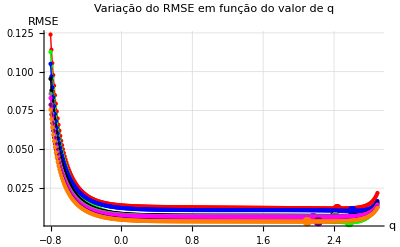

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;            (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=3;                                      (* Expoente de Weierstrass *)

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =10;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.01000001;
(*-----------------------------------------------------------------------------*)

graficos ={};
colors={Red,  Green,  Blue,  Black,  Gray,   Magenta,   Purple,  Orange,  Pink,  
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};

colors2={Red,  Green,  Blue,  Black,  Gray,  Cyan,  Magenta,  Yellow,  Brown,  Orange,  Pink,  Purple,
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};
numColors=Length[colors];
currentColor=1;

RMSList={};

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
colorMark=Graphics[ListPlot[{{0,0}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{"●"},Axes->False,ImageSize->{20,20} ]];
Print["k=",k0 ,", ni=",ni, ", cor=",colorMark ];
(* Limpa as listas *)
QValues={};
RMSEValues={};
plotlist={};
minimo = 10000;
qMinValue=0;
minimo1=10000;
qVectorIndex = 1;
For[qi = QI,qi≤QF,qi+=incrementoQ,
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)
(*Clear[WeierstrassFunction,PTX0,PTS0,PTY0,splineClassica,QSpline,points0,PTX1,PTS1,PTY1,points1,spC0,spC1];*)

(*WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* b^a ]/(Pi*b^a),{b,250}]];*)
(*WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
(*points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];*)

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
(*points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];*)

(* 5) Visualização da spline clássica *)
(*spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];*)
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
(*spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];*)

(*Print["  Q=",qi,", RMSE: ", RMSE[PTS1,PTY1]];*)

(*Show[WS,spC0,spC1,points1,points0]//Print;*)
QValues = Append[QValues,qi];
res =RMSE[PTY1,PTS1];

RMSEValues= Append[RMSEValues,res];

plotlist= Append[plotlist,{qi, res}];
(*Print[plotlist]*)
(*Print[RMSEValues]*)
(*Print["Comparando minimo =[",minimo,"] e RMSEValues[",qVectorIndex,"]=[",RMSEValues[[qVectorIndex]],"]"];*)
If[qVectorIndex == 1,
minimo=RMSEValues[[qVectorIndex]];
qMinValue = qi;
(*Print["    qi==QI"];*)
,
If[minimo>RMSEValues[[qVectorIndex]],
(*Print["    Minimo>RMSEValues[qVectorIndex]"];*)
minimo = RMSEValues[[qVectorIndex]];
qMinValue = qi;
,
(*Print["    OK: Minimo<RMSEValues[qi]"];*)
];
];

If[(minimo1==10000 )&& Round[qi]==1,
minimo1 = RMSEValues[[qVectorIndex]];
,];
(*Print["    minimo=",minimo];*)
qVectorIndex++;
];

(*minimo = Min[RMSEValues];*)

Print["     Mínimo em Q= ", qMinValue,": [", minimo,"]. Valor para Q=1: [",minimo1,"], relação V1/Vq = ",(minimo1/minimo)];
colorMark=Graphics[ListPlot[{{qMinValue,minimo}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{Style["●",fontsize-3]},Axes->False,ImageSize->{20,20} ]];

gi={ListPlot[plotlist,GridLines->Automatic,PlotLabel->"Variação do RMSE em função do valor de q",PlotStyle->{colors[[currentColor]]},PlotRange->All,AxesOrigin->{0,0}] ,colorMark, Graphics[{colors[[currentColor]],Line[plotlist]}, PlotRange->{{QI-incrementoQ, QF+incrementoQ},{0,0.0023}},AxesOrigin->{0,0}]};
graficos = Append[graficos, gi];
RMSList = Append[RMSList,RMSEValues];(* Salva a lista de RMSE para cada valor de N (ni). *)
(*Show[ ListPlot[plotlist,Filling->Axis,PlotStyle->{Blue}] ,
Graphics[Line[plotlist]]]//Print;*)
currentColor += 1;
];
Show[graficos, AxesLabel->{Style["q",fontsize], Style["RMSE",fontsize]},AxesStyle->{Directive[Black,fontsize],Directive[Black,fontsize]}]
```

k=4, ni=3, cor=-Graphics-

Mínimo em Q= 2.77: [0.00221622]. Valor para Q=1: [0.0100603], relação V1/Vq = 4.53936

k=4, ni=4, cor=-Graphics-

Mínimo em Q= 2.56: [0.00102723]. Valor para Q=1: [0.00455476], relação V1/Vq = 4.43404

k=4, ni=5, cor=-Graphics-

Mínimo em Q= 2.4: [0.00227773]. Valor para Q=1: [0.00359999], relação V1/Vq = 1.58052

k=4, ni=6, cor=-Graphics-

Mínimo em Q= 2.16: [0.00442828]. Valor para Q=1: [0.00475946], relação V1/Vq = 1.07479

k=4, ni=7, cor=-Graphics-

Mínimo em Q= 1.84: [0.00476734]. Valor para Q=1: [0.00489428], relação V1/Vq = 1.02663

k=4, ni=8, cor=-Graphics-

Mínimo em Q= 0.640001: [0.0000225684]. Valor para Q=1: [0.000230327], relação V1/Vq = 10.2057

k=4, ni=9, cor=-Graphics-

Mínimo em Q= 1.16: [0.00438781]. Valor para Q=1: [0.00448917], relação V1/Vq = 1.0231

k=4, ni=10, cor=-Graphics-

Mínimo em Q= 1.22: [0.00416121]. Valor para Q=1: [0.00423011], relação V1/Vq = 1.01656

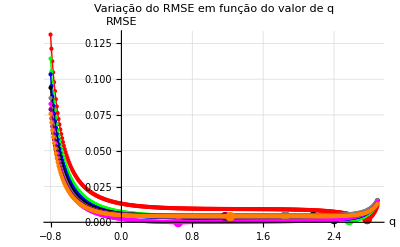

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;            (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=4;                                      (* Expoente de Weierstrass *)

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =10;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.01000001;
(*-----------------------------------------------------------------------------*)

graficos ={};
colors={Red,  Green,  Blue,  Black,  Gray,   Magenta,   Purple,  Orange,  Pink,  
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};

colors2={Red,  Green,  Blue,  Black,  Gray,  Cyan,  Magenta,  Yellow,  Brown,  Orange,  Pink,  Purple,
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};
numColors=Length[colors];
currentColor=1;

RMSList={};

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
colorMark=Graphics[ListPlot[{{0,0}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{"●"},Axes->False,ImageSize->{20,20} ]];
Print["k=",k0 ,", ni=",ni, ", cor=",colorMark ];
(* Limpa as listas *)
QValues={};
RMSEValues={};
plotlist={};
minimo = 10000;
qMinValue=0;
minimo1=10000;
qVectorIndex = 1;
For[qi = QI,qi≤QF,qi+=incrementoQ,
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)
(*Clear[WeierstrassFunction,PTX0,PTS0,PTY0,splineClassica,QSpline,points0,PTX1,PTS1,PTY1,points1,spC0,spC1];*)

(*WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* b^a ]/(Pi*b^a),{b,250}]];*)
(*WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
(*points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];*)

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
(*points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];*)

(* 5) Visualização da spline clássica *)
(*spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];*)
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
(*spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];*)

(*Print["  Q=",qi,", RMSE: ", RMSE[PTS1,PTY1]];*)

(*Show[WS,spC0,spC1,points1,points0]//Print;*)
QValues = Append[QValues,qi];
res =RMSE[PTY1,PTS1];

RMSEValues= Append[RMSEValues,res];

plotlist= Append[plotlist,{qi, res}];
(*Print[plotlist]*)
(*Print[RMSEValues]*)
(*Print["Comparando minimo =[",minimo,"] e RMSEValues[",qVectorIndex,"]=[",RMSEValues[[qVectorIndex]],"]"];*)
If[qVectorIndex == 1,
minimo=RMSEValues[[qVectorIndex]];
qMinValue = qi;
(*Print["    qi==QI"];*)
,
If[minimo>RMSEValues[[qVectorIndex]],
(*Print["    Minimo>RMSEValues[qVectorIndex]"];*)
minimo = RMSEValues[[qVectorIndex]];
qMinValue = qi;
,
(*Print["    OK: Minimo<RMSEValues[qi]"];*)
];
];

If[(minimo1==10000 )&& Round[qi]==1,
minimo1 = RMSEValues[[qVectorIndex]];
,];
(*Print["    minimo=",minimo];*)
qVectorIndex++;
];

(*minimo = Min[RMSEValues];*)

Print["     Mínimo em Q= ", qMinValue,": [", minimo,"]. Valor para Q=1: [",minimo1,"], relação V1/Vq = ",(minimo1/minimo)];
colorMark=Graphics[ListPlot[{{qMinValue,minimo}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{Style["●",fontsize-3]},Axes->False,ImageSize->{20,20} ]];

gi={ListPlot[plotlist,GridLines->Automatic,PlotLabel->"Variação do RMSE em função do valor de q",PlotStyle->{colors[[currentColor]]},PlotRange->All,AxesOrigin->{0,0}] ,colorMark, Graphics[{colors[[currentColor]],Line[plotlist]}, PlotRange->{{QI-incrementoQ, QF+incrementoQ},{0,0.0023}},AxesOrigin->{0,0}]};
graficos = Append[graficos, gi];
RMSList = Append[RMSList,RMSEValues];(* Salva a lista de RMSE para cada valor de N (ni). *)
(*Show[ ListPlot[plotlist,Filling->Axis,PlotStyle->{Blue}] ,
Graphics[Line[plotlist]]]//Print;*)
currentColor += 1;
];
Show[graficos, AxesLabel->{Style["q",fontsize], Style["RMSE",fontsize]},AxesStyle->{Directive[Black,fontsize],Directive[Black,fontsize]}]
```

k=5, ni=3, cor=-Graphics-

Mínimo em Q= 2.65: [0.00539133]. Valor para Q=1: [0.00852444], relação V1/Vq = 1.58114

k=5, ni=4, cor=-Graphics-

Mínimo em Q= 2.56: [0.00102418]. Valor para Q=1: [0.00449543], relação V1/Vq = 4.38931

k=5, ni=5, cor=-Graphics-

Mínimo em Q= 2.31: [0.00289251]. Valor para Q=1: [0.00380107], relação V1/Vq = 1.31411

k=5, ni=6, cor=-Graphics-

Mínimo em Q= 2.35: [0.00188766]. Valor para Q=1: [0.00282908], relação V1/Vq = 1.49872

k=5, ni=7, cor=-Graphics-

Mínimo em Q= 2.21: [0.000505213]. Valor para Q=1: [0.00165875], relação V1/Vq = 3.28326

k=5, ni=8, cor=-Graphics-

Mínimo em Q= 2.09: [0.000285847]. Valor para Q=1: [0.00129168], relação V1/Vq = 4.51876

k=5, ni=9, cor=-Graphics-

Mínimo em Q= 1.99: [0.000328426]. Valor para Q=1: [0.00111037], relação V1/Vq = 3.38088

k=5, ni=10, cor=-Graphics-

Mínimo em Q= 1.88: [0.000727188]. Valor para Q=1: [0.00116641], relação V1/Vq = 1.60401

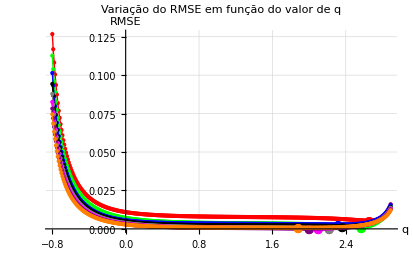

```mathematica
(* Parâmetros -----------------------------------------------------------------*)
fatorEscala = 2;            (* Fator de escala *)
(*n0=5; *)                             (* Número inicial de pontos *)
k0=5;                                      (* Expoente de Weierstrass *)

(* Intervalo de valores de N (número de pontos de interpolação) *)
NI = 3;      (* N inicial *)
NF =10;       (* N final *)
incrementoN = 1;

(* Intervalo de valores de Q *)
QI = -0.8;      (* Q inicial *)
QF = 2.9;       (* Q final *)
incrementoQ = 0.01000001;
(*-----------------------------------------------------------------------------*)

graficos ={};
colors={Red,  Green,  Blue,  Black,  Gray,   Magenta,   Purple,  Orange,  Pink,  
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};

colors2={Red,  Green,  Blue,  Black,  Gray,  Cyan,  Magenta,  Yellow,  Brown,  Orange,  Pink,  Purple,
LightRed,  LightGreen,  LightBlue,  LightGray,  LightCyan,  LightMagenta,  LightYellow,  LightBrown,  LightOrange,  LightPink,  LightPurple};
numColors=Length[colors];
currentColor=1;

RMSList={};

For[ni=NI,ni≤NF,ni+=incrementoN,
Print[];
colorMark=Graphics[ListPlot[{{0,0}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{"●"},Axes->False,ImageSize->{20,20} ]];
Print["k=",k0 ,", ni=",ni, ", cor=",colorMark ];
(* Limpa as listas *)
QValues={};
RMSEValues={};
plotlist={};
minimo = 10000;
qMinValue=0;
minimo1=10000;
qVectorIndex = 1;
For[qi = QI,qi≤QF,qi+=incrementoQ,
ni1 = ni*fatorEscala; (* Numero final de pontos *)
(* 1) Recria splines para a imagem original *)
(*Clear[WeierstrassFunction,PTX0,PTS0,PTY0,splineClassica,QSpline,points0,PTX1,PTS1,PTY1,points1,spC0,spC1];*)

(*WeierstrassFunction[a_,x_]:=N[Sum[Sin[Pi*x* b^a ]/(Pi*b^a),{b,250}]];*)
(*WS=Plot[WeierstrassFunction[k0,x], {x, 0, 1}, PlotStyle->{Red,Thickness[0.001]}];(* Visualização para k=3*)*)

PTX0=Table[x/ni,{x,0,ni}];
PTS0= Table[WeierstrassFunction[k0,PTX0[[i]]],{i, 1, ni+1}];
PTY0= Table[WeierstrassFunction[k0,PTX0[[i]]/(PTX0[[ni+1]]-PTX0[[1]])],{i, 1, ni+1}];

(* 2) Cria vetores de funções (trechos da spline clássica e q-spline), gerado a partir dos pontos de controle. OBS.: Considerada derivada 0 nos pontos. *)
splineClassica[t_]:=Table[SplineHermite[{PTS0[[i]],PTS0[[i+1]],0,0}, t],{i,1,ni}];
QSpline[q_,t_]:=Table[QSplineI[{PTS0[[i]],PTS0[[i+1]],0,0},q,t],{i,1,ni}];

(* 3) Visualização dos pontos iniciais de interpolação *)
(*points0 = ListPlot[Table[{PTX0[[i]],PTY0[[i]]},{i, 1, ni+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Black}];*)

(* 4) Pontos a serem adicionados/interpolados *)
PTX1=Table[x/ni1,{x,0,ni1}];
PTS1= Table[WeierstrassFunction[k0,PTX1[[i]]],{i, 1, ni1+1}];
PTY1= Table[SNQ[PTX0,ni1,QSpline,qi,PTX1[[i]]/(PTX1[[ni1+1]]-PTX1[[1]])],{i, 1, ni1+1}];
(*points1 = ListPlot[Table[{PTX1[[i]],PTY1[[i]]},{i, 1, ni1+1}],Filling->Axis, PlotMarkers->{"●"}, PlotStyle->{Blue}];*)

(* 5) Visualização da spline clássica *)
(*spC0 = Plot[{SNH[PTX0,ni1,splineClassica,t]}, {t, 0,1},PlotStyle->{Blue,Thickness[0.003]}];*)
(*Show[WS,spC0,points0]*)

(* 6) Visualização da Q-spline *)
(*spC1 = Plot[{SNQ[PTX0,ni1,QSpline,qi,t]}, {t, 0,1},PlotStyle->{Purple,Thickness[0.003]}];*)

(*Print["  Q=",qi,", RMSE: ", RMSE[PTS1,PTY1]];*)

(*Show[WS,spC0,spC1,points1,points0]//Print;*)
QValues = Append[QValues,qi];
res =RMSE[PTY1,PTS1];

RMSEValues= Append[RMSEValues,res];

plotlist= Append[plotlist,{qi, res}];
(*Print[plotlist]*)
(*Print[RMSEValues]*)
(*Print["Comparando minimo =[",minimo,"] e RMSEValues[",qVectorIndex,"]=[",RMSEValues[[qVectorIndex]],"]"];*)
If[qVectorIndex == 1,
minimo=RMSEValues[[qVectorIndex]];
qMinValue = qi;
(*Print["    qi==QI"];*)
,
If[minimo>RMSEValues[[qVectorIndex]],
(*Print["    Minimo>RMSEValues[qVectorIndex]"];*)
minimo = RMSEValues[[qVectorIndex]];
qMinValue = qi;
,
(*Print["    OK: Minimo<RMSEValues[qi]"];*)
];
];

If[(minimo1==10000 )&& Round[qi]==1,
minimo1 = RMSEValues[[qVectorIndex]];
,];
(*Print["    minimo=",minimo];*)
qVectorIndex++;
];

(*minimo = Min[RMSEValues];*)

Print["     Mínimo em Q= ", qMinValue,": [", minimo,"]. Valor para Q=1: [",minimo1,"], relação V1/Vq = ",(minimo1/minimo)];
colorMark=Graphics[ListPlot[{{qMinValue,minimo}},PlotStyle->{colors[[currentColor]]},PlotMarkers->{Style["●",fontsize-3]},Axes->False,ImageSize->{20,20} ]];

gi={ListPlot[plotlist,GridLines->Automatic,PlotLabel->"Variação do RMSE em função do valor de q",PlotStyle->{colors[[currentColor]]},PlotRange->All,AxesOrigin->{0,0}] ,colorMark, Graphics[{colors[[currentColor]],Line[plotlist]}, PlotRange->{{QI-incrementoQ, QF+incrementoQ},{0,0.0023}},AxesOrigin->{0,0}]};
graficos = Append[graficos, gi];
RMSList = Append[RMSList,RMSEValues];(* Salva a lista de RMSE para cada valor de N (ni). *)
(*Show[ ListPlot[plotlist,Filling->Axis,PlotStyle->{Blue}] ,
Graphics[Line[plotlist]]]//Print;*)
currentColor += 1;
];
Show[graficos, AxesLabel->{Style["q",fontsize], Style["RMSE",fontsize]},AxesStyle->{Directive[Black,fontsize],Directive[Black,fontsize]}]
```